```mathematica
Convolve[HeavisideTheta[-t],HeavisideTheta[-t],t,x]
```

-x HeavisideTheta[-x]

```mathematica
FourierTransform[DiracDelta[t-2],t,x]
```

ⅇ^(2 ⅈ x)/(√(2 π))

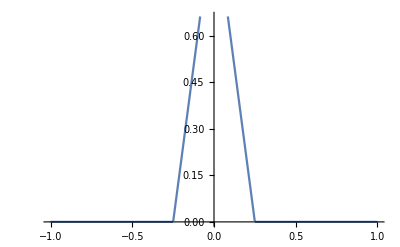

```mathematica
Plot[(1-4*Abs[x])*(HeavisideTheta[2x+0.5]-HeavisideTheta[2x-0.5]),{x,-1,1}]
```

```mathematica
FourierTransform[(Sin[20t]+Sin[30t])/Pi*t,t,x]
```

DiracDelta'[-30+x]/(√(2 π))+DiracDelta'[-20+x]/(√(2 π))-DiracDelta'[20+x]/(√(2 π))-DiracDelta'[30+x]/(√(2 π))

```mathematica
Apart[Factor[(s^2+4)/((s+6)*(s-5)),Extension->Sqrt[I]]]
```

1+29/(11 (-5+s))-40/(11 (6+s))

```mathematica
FourierTransform[Cos[100*t],t,x]
```

√(π/2) DiracDelta[-100+x]+√(π/2) DiracDelta[100+x]

```mathematica
FourierTransform[Cos[100*t+p],t,x]
```

ⅇ^(-ⅈ p) √(π/2) DiracDelta[-100+x]+ⅇ^(ⅈ p) √(π/2) DiracDelta[100+x]